```mathematica
c=2.99792458*10^10;
pc=3.08568*10^18;Mpc=pc*10^6;kpc=10^3*pc;
yr=3600*24*365;
ev=1.6/10^12;
barn=10^-24;
Y=0.24; X=1-Y;
μ=4/(4-3Y);xh=4X/(1+3X);
G=6.674/10^8;
H00=100*10^5/pc/10^6;
kB=1.3806/10^16;
mp=1.6726/10^24;
me=9.10938356/10^28;
hbar=1.05457266/10^27; planck=hbar*2*Pi;
charge=4.80320451/10^10;
Rsun=6.96392*10^10;
Msun=1.989*10^33;
Lsun=3.828*10^33;
re=charge^2/(me*c^2);
σ=8*Pi*re^2/3;
```

```mathematica
Om=0.315;(*0.3089*)
Ob=0.048;
OR=9.5425/10^5(*9.35/10^5*);
h=0.6774;
H0=H00*h; 
H[a_]:=H0*(Om/a^3+OR/a^4+(1-Om-OR))^0.5;
t[a_]:=NIntegrate[1/x/H[x],{x,0,a}];
scale[time_]:=a/.FindRoot[t[a]==time,{a,0}];
dz[z_]:=c*NIntegrate[1/x^2/H[x],{x,1/(1+z),1}];
da[a_]:=c*NIntegrate[1/x^2/H[x],{x,a,1}];
Omf[a_]:=H0^2*Om/a^3/H[a]^2;
ORf[a_]:=H0^2*OR/a^4/H[a]^2;
rhom[a_]:=(3/8/Pi/G)*H0^2*Om/a^3;
rhob[a_]:=(3/8/Pi/G)*H0^2*Ob/a^3;
g[a_]:=2.5*Omf[a]/(Omf[a]^(4/7)-(1-Omf[a]-ORf[a])+(1+Omf[a]/2)*(1+(1-Omf[a]-ORf[a])/70));
perturbation[a_]:=g[a]*a/g[1];
```

13.7307

14.4444

{3300.02}

{0.295338}

4425.63

14068.7

NIntegrate::nlim: x = a is not a valid limit of integration.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

40.1063

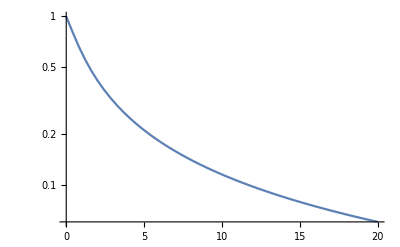

14844.7

```mathematica
tPlanck=t[1]/yr/10^9
tH=1/H0/yr/10^9
1/(x/.NSolve[Omf[x]==ORf[x],x])-1
1/(x/.NSolve[Omf[x]+ORf[x]==0.5&&x>0,x,Reals])-1
DH=c/H0/Mpc
RC=da[0]/Mpc
znl=49;
tff=(3*Pi/32/(200*rhob[1/(1+znl)]*G))^0.5;
1/scale[t[1/(1+znl)]+tff]-1;
rhom[1]*Mpc^3/Msun/10^9
LogPlot[perturbation[1/(1+z)],{z,0,20},PlotRange->Full]
((da[1/101]^3-da[1/21]^3)*4*Pi/3/Mpc^3)^(1/3)
```

```mathematica
T0=Table[{dz[i]/Mpc,i},{i,0,10,10.0/10000}];
T1=Table[{t[1/(1+i)]/yr/10^6,i},{i,0,10,10.0/10^4}];
Export["t_z_Planck.txt",T1,"table"];
Export["d_z_Planck.txt",T0,"table"];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["d_z_Planck.txt"]]]
```

```mathematica
Omc=0.3;
hc=0.7;
H0c=H00*hc ; 
Hc[a_]:=H0c*(Omc/a^3+OR/a^4+(1-Omc-OR))^0.5;
tc[a_]:=NIntegrate[1/x/Hc[x],{x,0,a}];
scalec[time_]:=a/.FindRoot[tc[a]==time,{a,0}];
dzc[z_]:=c*NIntegrate[1/x^2/Hc[x],{x,1/(1+z),1}];
Omfc[a_]:=H0c^2*Omc/a^3/Hc[a]^2;
ORfc[a_]:=H0c^2*OR/a^4/Hc[a]^2;
```

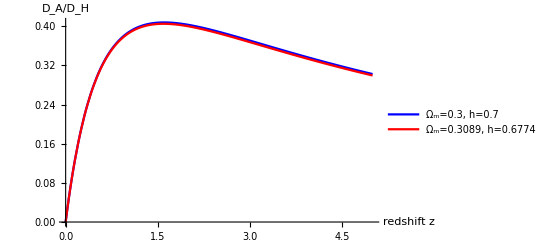

```mathematica
Plot[{dzc[z]/(1+z)/(c/H0c),dz[z]/(1+z)/(c/H0)},{z,0,5},PlotStyle->{Blue,Red},PlotLegends->Placed[{"Ω_m=0.3, h=0.7","Ω_m=0.3089, h=0.6774"},Bottom],AxesLabel->{"redshift z","D_A/D_H"},PlotRange->Full]
```

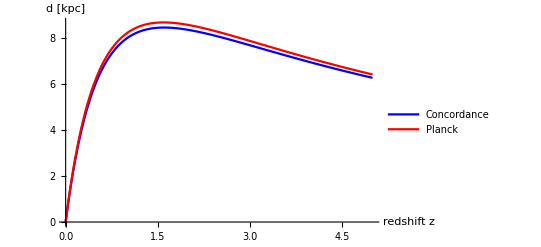

```mathematica
Plot[{(Pi/180/60/60)*dzc[z]/(1+z)/(1000*pc),(Pi/180/60/60)*dz[z]/(1+z)/(1000*pc)},{z,0,5},PlotStyle->{Blue,Red},PlotLegends->Placed[{"Concordance","Planck"},Bottom],AxesLabel->{"redshift z","d [kpc]"},PlotRange->Full]
```

```mathematica
Vc=(4*Pi*(dzc[3]^3-dzc[2]^3)/3)*2/(4Pi/(Pi/180)^2)/Mpc^3
```

2.39409×10^7

```mathematica
FindRoot[4*Pi*dzc[z]^3/3/Mpc^3==Vc,{z,1}]
```

NIntegrate::nlim: x = 1/(1.+z) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{z→0.0421212}

```mathematica
FindRoot[t[1/(1+z)]/yr/10^9/tPlanck==0.5,{z,1}]
```

NIntegrate::nlim: x = 1/(1.+z) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{z→0.775191}

```mathematica
FindRoot[t[1/(1+z)]/yr/10^9/tPlanck==0.25,{z,1}]
```

NIntegrate::nlim: x = 1/(1.+z) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{z→1.90049}

```mathematica
FindRoot[t[1/(1+z)]/yr/10^9/tPlanck==0.1,{z,1}]
```

NIntegrate::nlim: x = 1/(1.+z) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{z→4.38335}

```mathematica
FindRoot[t[1/(1+z)]/yr/10^9==1,{z,1}]
```

NIntegrate::nlim: x = 1/(1.+z) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{z→5.67745}

```mathematica
T1={{0.775191,0.5*tPlanck},{1.90049,0.75*tPlanck},{4.38335,0.9*tPlanck},{5.67745,tPlanck-1}}
```

{{0.775191,6.90321},{1.90049,10.3548},{4.38335,12.4258},{5.67745,12.8064}}

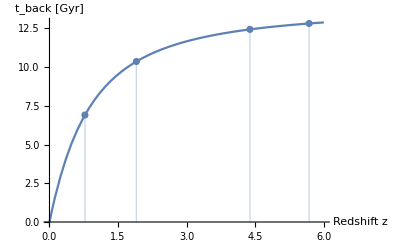

```mathematica
Show[Plot[(t[1]-t[1/(1+z)])/yr/10^9,{z,0,6},AxesLabel->{"Redshift z","t_back [Gyr]"}],ListPlot[T1,Filling->Axis,PlotRange->{{0,6},{0,13}}]]
```